# 第7章 在Mathematica中作图

## §7 .5 用图元作图

### 1. 二维图形元素作图

Graphics[primitives, options]  表示一个二维图形.

二维图形元素有

AASTriangle[α, β, a]       角边角三角形

Arrow[{{x1, y1}, …}]	箭头

ASATriangle[α, c, β]       角边角三角形

BezierCurve[{pt1, pt2, …}]	Bézier 曲线

BSplineCurve[{pt1, pt2, …}]	B 样条曲线

Circle[{x, y}, r]         圆

Circumsphere[{pt1, …}]	由三个点指定的外接圆

ConicHullRegion[…]	线性椎体

Disk[{x, y}, r]填充圆盘

FilledCurve[{seg1, seg2, …}]	填充曲线

GraphicsComplex[pts, prims]	图形对象的复合体

GraphicsGroup[{g1, g2, …}]	可作为群组选择的对象

HalfLine[{pt1, pt2}]    半无限长的直线，或称射线

HalfPlane[{pt1, pt2}, v]	半无限平面

InfiniteLine[{pt1, pt2}]	无限长直线

Inset[obj, …]    插入对象

JoinedCurve[{seg1, seg2, …}]	连接的曲线段

Line[{pt1, …}]线段

Locator[{x, y}]   动态定位器

Parallelogram[pt, {v1, v2}]	平行四边形

Point[{x, y}]       点

Polygon[{pt1, …}]     多边形

Raster[array]     灰色或颜色方块的数组

Rectangle[{xmin, ymin}, {xmax, ymax}]	矩形

SASTriangle[a, γ, b]    边角边三角形

Simplex[{pt1, …}]  单纯形

SSSTriangle[a, b, c]    边边边三角形

Text[expr, {x, y}]   文本

Triangle[{pt1, …}]    三角形

```mathematica
图形指令可选项
```

AbsoluteDashing[{w1, …}]      指定绝对虚线

AbsolutePointSize[d]               指定绝对点的尺寸

AbsoluteThickness[w]             指定绝对线宽

Arrowheads[specs]                   指定箭头

CapForm[type]                           线帽指定

CMYKColor[c, m, y, k]               指定颜色

Dashing[{w1, …}]                       指定虚线

Directive[g1, g2, …]                   复合图形指令

EdgeForm[g]                               指定绘制边

FaceForm[g]                                指定绘制面

GrayLevel[i]                                 灰度指定

Hue[h]                                            色调指定

JoinForm[type]                          线连接指定

Opacity[a]                                     透明度指定

PointSize[d]                                 点尺寸指定

RGBColor[r, g, b]                        颜色指定

Texture[obj]                                纹理指定

Thickness[w]                               线宽指定

图形指令通常作用于之后所有图形，只对应一个图元的指令应与图元函数放在一个大括号中. 指令可以指定面的颜色和透明度, 颜色、粗细和虚线指令会影响线条、箭头和边.

(1) 带箭头折线

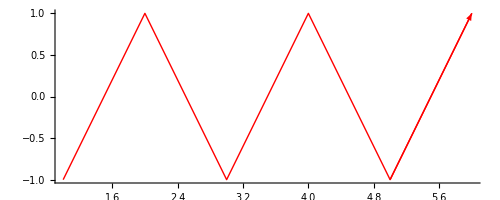

```mathematica
tab = Table[{n, (-1)^n}, {n, 6}];
Graphics[{Thick, Red, Line[tab], Arrow[{{5, -1}, {6, 1}}]},  Background -> None, Axes -> True]
```

(2)	正五角星

{{0,1},{-√(5/8+(√5)/8),1/4 (-1+√5)},{-√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8-(√5)/8),1/4 (-1-√5)},{√(5/8+(√5)/8),1/4 (-1+√5)},{0,1}}

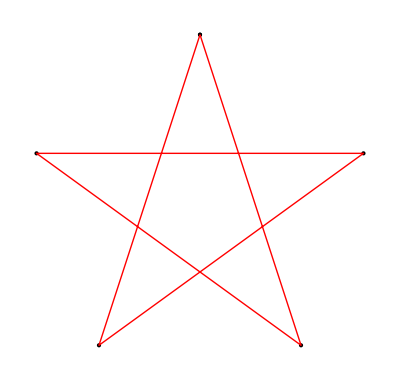

```mathematica
v=Table[ {Cos[t+Pi/2],Sin[t+Pi/2]},{t,0,2 Pi,2 Pi/5}]
Graphics[GraphicsComplex[v,{Point[{1,2,3,4,5,6}],Red,Thick,Line[{1,3,5,2,4,1}]}]]
```

GraphicsComplex[{pt1, pt2, …}, primitives] 实际上用相应的数据 pti 替换坐标整数 i.

在 Graphics 和 Graphics3D 中，GraphicsComplex 视为一个单一的图形基元. data 可以是图形基元和指令的任意嵌套列表.

{{1,0},{0,1},{-1,0},{0,-1}}

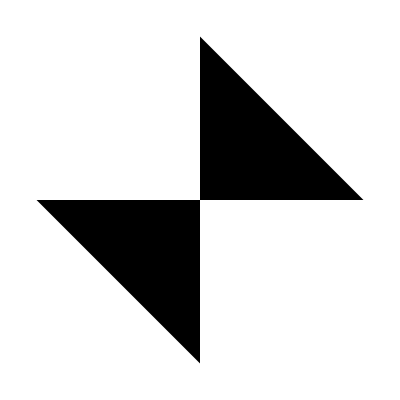
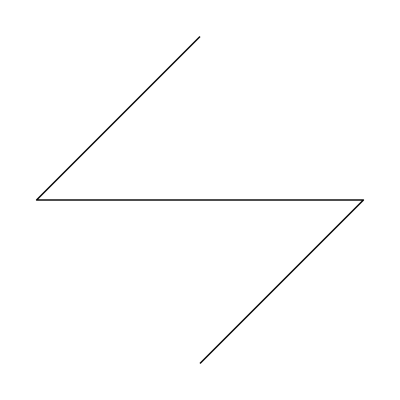

```mathematica
v = {{1, 0}, {0, 1}, {-1, 0}, {0, -1}}
{Graphics[GraphicsComplex[v, Polygon[{1, 3, 4, 2, 1}]]], 
 Graphics[GraphicsComplex[v, Line[{2, 3, 1, 4}]]]}
```

(3)	圆与圆盘

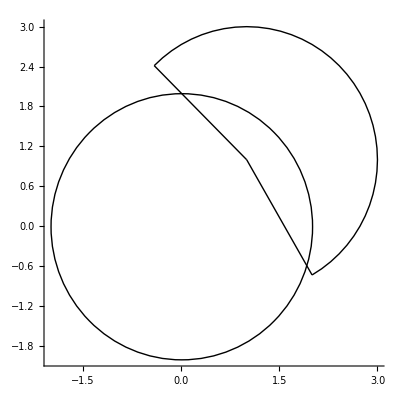

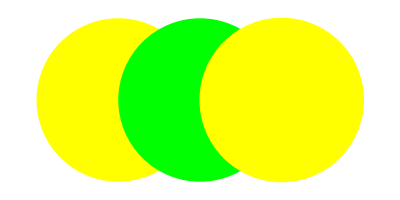

```mathematica
Graphics[{Circle[{0, 0}, 2], Circle[{1, 1}, 2, {-Pi/3, 3 Pi/4}], Line[{{1, 1}, {1 + 2 Cos[-Pi/3], 1 + 2 Sin[-Pi/3]}}], Line[{{1, 1}, {1 + 2 Cos[3 Pi/4], 1 + 2 Sin[3 Pi/4]}}]},  Axes -> True]

Graphics[{Yellow, Disk[], {Green, Disk[{1, 0}]}, EdgeForm[Dashed], Disk[{2, 0}]}]
```

(4) 图像画在圆盘中

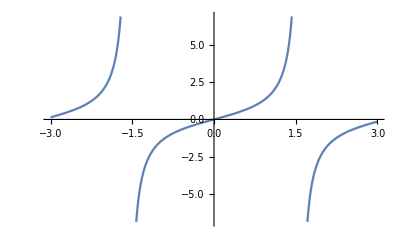

```mathematica
Graphics[{LightGray, Disk[], Inset[Plot[Tan[x], {x, -3, 3}]]}, 
 ImageSize -> Small]
```

(5) 格式设定例子

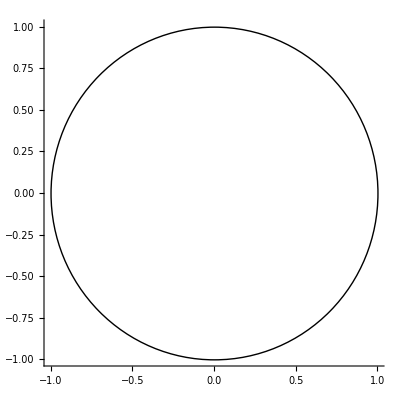

```mathematica
Graphics[Circle[], Axes -> True, AxesStyle -> {Directive[Dashed, Red], Blue}]
```

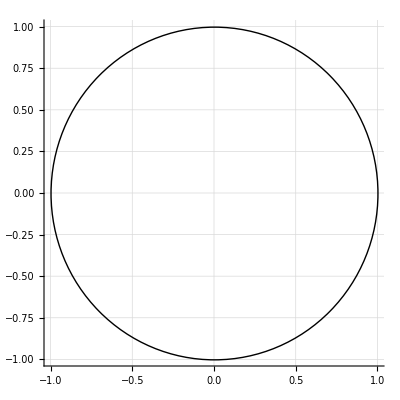

```mathematica
Graphics[Circle[], Axes -> True, GridLines -> Automatic,  GridLinesStyle -> Directive[Red, Dotted]]
```

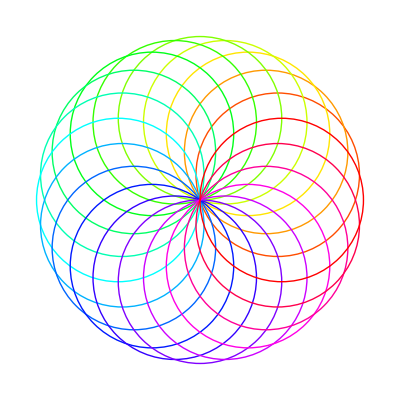

```mathematica
Graphics[ Table[{Hue[t/20], Circle[{Cos[2 Pi t/20], Sin[2 Pi t/20]}]}, {t, 20}]]
```

(6) 用栅格作为背景

```mathematica
r = Raster[ Table[{i, j}, {i, 20}, {j, 20}], {Scaled[{0, 0}], Scaled[{1, 1}]}, {1, 20}];
Plot[{Sin[x], Cos[x]}, {x, 0, 10}, Prolog -> r, PlotStyle -> Thick]
```

-Graphics-

### 2. 三维图元作图

Graphics3D[primitives, options]

Arrow[{pt1, pt2}]箭头

Ball[{x, y, z}, …]填充球

Cone[{pt1, pt2}, r]填充锥体

Cube[{x, y, z}, …]填充的立方体

Cuboid[{xmin, ymin, zmin}, …]填充立方体

Cylinder[{{x1, x2, x3}, …}, …]填充圆柱体

Dodecahedron[{x, y, z}, …]填充十二面体

GraphicsComplex[pts, prims]图形对象的复合体

GraphicsGroup[{g1, g2, …}]被视为群组的对象

Hexahedron[{pt1, …}]填充六面体

Icosahedron[{x, y, z}, …]填充二十面体

InfinitePlane[{pt1, pt2, pt2}]无限平面

Inset[obj, …]插入对象

JoinedCurve[{seg1, seg2, …}]连接的曲线段

Line[{pt1, …}]直线

Octahedron[{x, y, z}, …]填充八面体

Point[{x, y, z}]点

Polygon[{pt1, …}]多边形

Polyhedron[{pt1, …}]多面体

Prism[{pt1, …}]棱柱

Pyramid[{pt1, …}]棱锥

Raster3D[array]由灰色或彩色单元组成的三维数组

Sphere[{x, y, z}, …]球体

Text[expr, {x, y, z}]文本

Tube[{pt1, …}]管

（1）	多面体

```mathematica
Table[Graphics3D[{LightBlue, Opacity[.8],   PolyhedronData[p, "GraphicsComplex"]}], {p, {"Dodecahedron",   "Icosahedron", "TruncatedIcosahedron"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

(2)图形组合

```mathematica
Graphics3D[{Blue, Cylinder[], Red, Sphere[{0, 0, 2}], Green,   Opacity[.3], Cuboid[{-2, -2, -2}, {2, 2, -1}]}]
```

-Graphics3D-

(3)根据顶点坐标画多面体

```mathematica
v = {{-1/2, -1/2, 0}, {-1/2, 1/2, 0}, {0, 0, -(1/Sqrt[2])}, {0, 0, 1/Sqrt[2]}, {1/2, -1/2, 0}, {1/2, 1/2, 0}};
Graphics3D[ GraphicsComplex[v, Polygon[{{4, 5, 6}, {4, 6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, {3, 1, 2}, {6, 3, 2}}]]]
```

-Graphics3D-

(4)	样式设定

```mathematica
Table[Graphics3D[{Blue, Specularity[White, n], Sphere[]}], {n, {5, 20, 100}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

边界曲线设定

```mathematica
{Graphics3D[Cylinder[]], Graphics3D[{EdgeForm[Thick], Cylinder[]}],  Graphics3D[{EdgeForm[Directive[Thick, Dashed, Blue]], Cylinder[]}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

表面样式

```mathematica
Graphics3D[{FaceForm[Yellow, Blue], Cuboid[]}, PlotRange -> {{-1/4, 5/4}, {1/4, 5/4}, {-1/4, 5/4}}]
```

-Graphics3D-

## §7 .6 特殊作图命令

### 1. 根据数据作图

(1) 柱形图 与直方图

柱状图比较数据的大小, X轴为分类数据。柱状图上的每根柱子是可以随意排序的，有的情况下需要按照分类数据的名称排列，有的则需要按照数值的大小排列. 柱状图柱子的宽度因为没有数值含义，所以宽度必须一致.

  直方图展示数据的分布， X轴为定量数据，因此，直方图上的每根柱子都是不可移动的，X轴上的区间是连续的、固定的。柱子宽度可不一,  在直方图中，柱子的宽度代表了区间的长度，根据区间的不同，柱子的宽度可以不同，但理论上应为单位长度的倍数。

BarChart[{y1, y2, …, yn}]         条形图，其中条形长度为 y1、y2、….

BarChart[{…, wi[yi, …], …, wj[yj, …], …}] 条形特征由符号封装 wk 定义.

BarChart[{data1, data2, …}]   从多个数据集 datai 得到一个条形图.

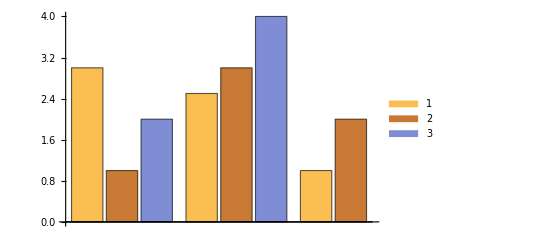

```mathematica
BarChart[{{3, 1, 2}, {2.5, 3, 4}, {1, 2}}, ChartLegends -> Automatic]
```

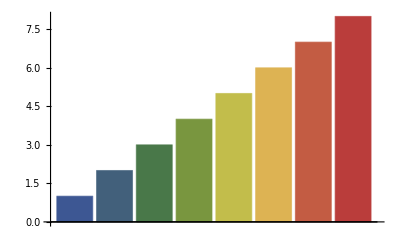

```mathematica
BarChart[Range[8], ChartStyle -> "DarkRainbow"]
```

非实数数据被认为是缺失的，通常在条形图中产生一个空隙

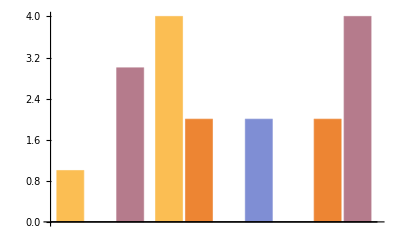

```mathematica
BarChart[{{1, Missing[], 3}, {4, 2, 1 + I, 2}, {foo, 2, 4}}]
```

数据可以含有单位，或转换成指定单位

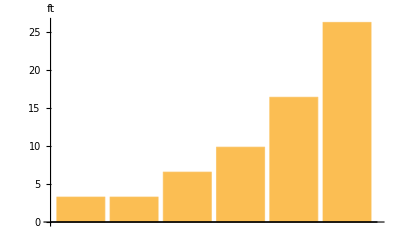

```mathematica
BarChart[{Quantity[1, "Meters"], Quantity[1, "Meters"], 
  Quantity[2, "Meters"], Quantity[3, "Meters"], Quantity[5, "Meters"],
   Quantity[8, "Meters"]}, AxesLabel -> Automatic, 
 TargetUnits -> "Feet"]
```

Histogram[{x1, x2, …}]                      绘制值 xi 的直方图.

Histogram[{x1, x2, …}, bspec]           绘制组距规范为 bspec 的直方图.

Histogram[{x1, x2, …}, bspec, hspec] 根据规范 hspec 计算直方条的高度.

Histogram[{data1, data2, …}, …]   绘制多个数据集 datai 的直方图.

```mathematica
data1 = RandomVariate[NormalDistribution[0, 1], 500];
data2 = RandomVariate[NormalDistribution[4, 2], 500];
```

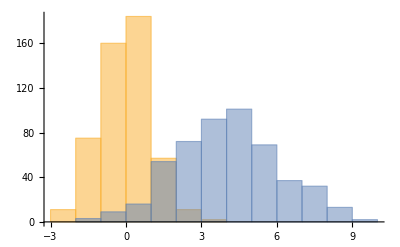

```mathematica
Histogram[{data1, data2}]
```

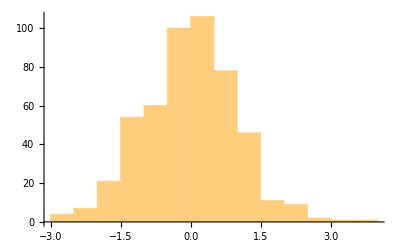
指定组数 -Graphics-

```mathematica
Histogram[data1, 15]    指定组数
```

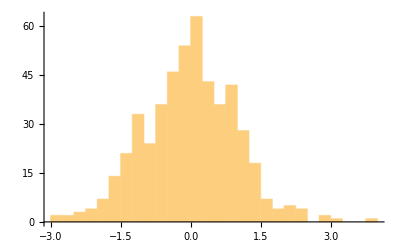
指定组距 -Graphics-

```mathematica
Histogram[data1, {0.25}] 指定组距
```

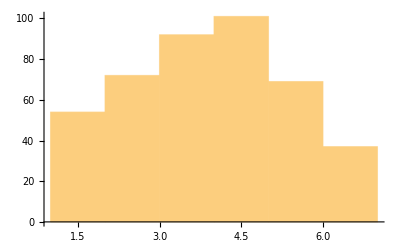

```mathematica
Histogram[data2, {{1, 2, 3, 4, 5 , 6, 7}}]
```

以显式列表形式指定分组界限

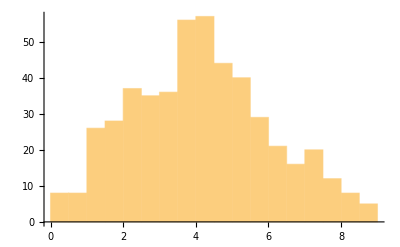
按步长分组 -Graphics-

```mathematica
Histogram[data2, {0, 9, 0.5}] 按步长分组
```

使用不同的高度规范

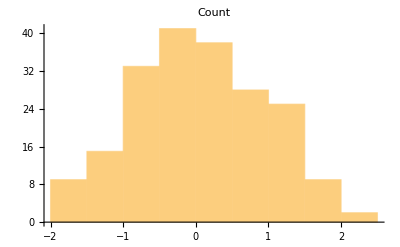
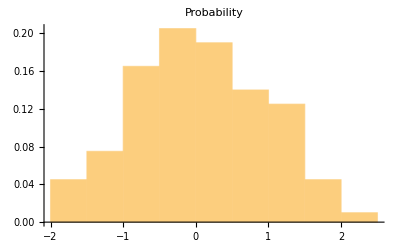
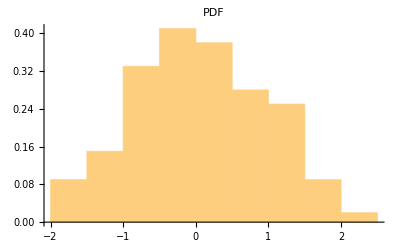
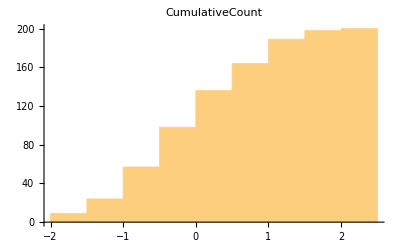
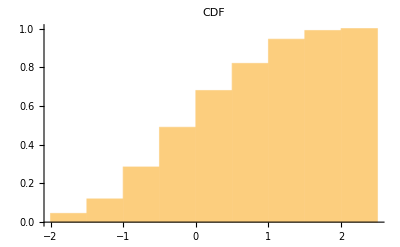
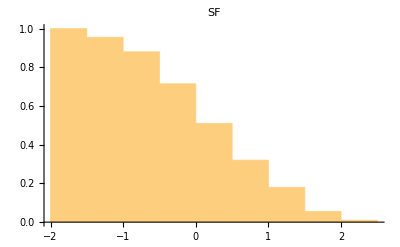

```mathematica
data = RandomVariate[NormalDistribution[0, 1], 200];
Table[Histogram[data, Automatic, h,   PlotLabel -> h], {h, {"Count", "Probability", "PDF",    "CumulativeCount", "CDF", "SF"}}]
```

在上方标注数据

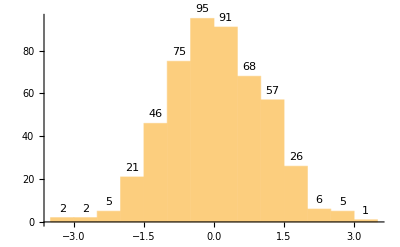

```mathematica
Histogram[RandomVariate[NormalDistribution[0, 1], 500],  LabelingFunction -> Above]
```

控制直方条的原点

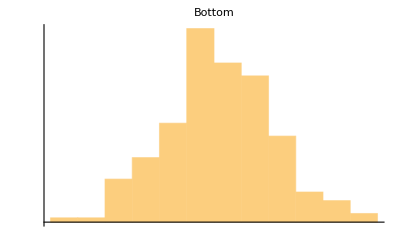
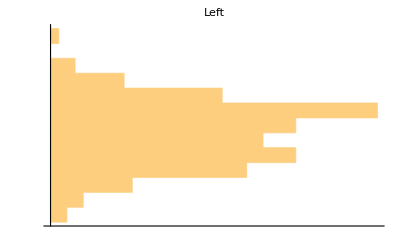
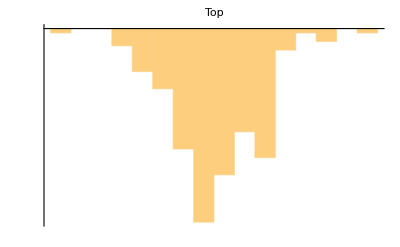
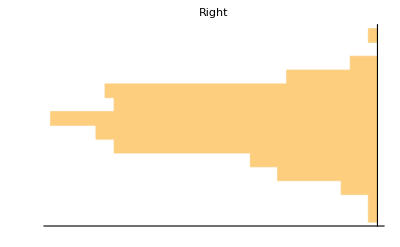

```mathematica
Table[Histogram[RandomVariate[NormalDistribution[0, 1], 200],   BarOrigin -> o, PlotLabel -> o,   Ticks -> None], {o, {Bottom, Left, Top, Right}}]
```

### （2） 饼图和扇形图

PieChart[{y1, y2, …, yn}] 绘制一个饼图，其扇区角度与 y1、y2、… 成比例.

PieChart[{data1, data2, …}] 根据多个数据集 datai 绘制饼图.

PieChart3D[{data1, data2, …}] 根据多个数据集 datai 绘制一个三维饼图.

SectorOrigin选项，指定扇形的开始位置.

```mathematica
PieChart[{1, 2, 3, 4}]
```

-Graphics-

```mathematica
PieChart[{{2, 2, 3}, {1,3,2}}]
```

-Graphics-

```mathematica
PieChart[{{2, 2, 3}, {1,3,2}}, ChartLayout -> "Stacked"]
```

-Graphics-

```mathematica
PieChart3D[{{1, 2, 3, 4}, {1, 1, 1}}]
```

-Graphics3D-

SectionOrigin -> {{pos, sense}, r} 指定扇形应有内部半径 r, pos指定第一个扇形位置， sense = 1 逆时针， sense = -1 顺时针

```mathematica
Table[PieChart[{1, 2, 3}, 
  SectorOrigin -> {{k, -1}, r}], {r, {1, 2}}, {k, {0, Pi/2, Pi}}]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

添加标签 图例

```mathematica
PieChart[{{1, 2, 3}, {2, 1}}, ChartLabels -> {"a", "b", "c"}]
```

-Graphics-

```mathematica
PieChart[{{1, 2, 3}, {1, 2, 2, 1}}, ChartLegends -> {"a", "b", "c"}]
```

-Graphics-

SectorChart[{{x1, y1}, {x1, y2}, …}]
制作一个扇形图表，其扇形角和 xi 成比例，并且有半径 yi.

SectorChart[{data1, data2, …}] 绘制多个数据集 datai 的一个扇形图表.

```mathematica
SectorChart[{{1, 1}, {1, 2}, {1, 3}}]
```

-Graphics-

```mathematica
SectorChart[{{1, 1}, {1, 2}, {1, 3}}, SectorOrigin -> {Automatic, 1}]
```

-Graphics-

```mathematica
SectorChart[{{{1, 1}, {2, 2}, {3, 3}}, {{7, 3}, {5, 2}, {3, 1}}}]
```

-Graphics-

```mathematica
SectorChart[{{1, 1}, {1, 2}, {1, 3}}, ChartLabels -> {"a", "b", "c"}]
```

-Graphics-

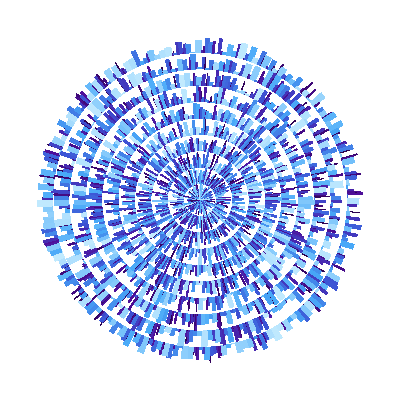

```mathematica
SectorChart[RandomReal[10, {10, 300, 2}],  ColorFunction -> "DeepSeaColors", PerformanceGoal -> "Speed",  ChartStyle -> EdgeForm[None]]
```

### 2. 画区域图

RegionPlot[pred, {x, xmin, xmax}, {y, ymin, ymax}] 画图来显示 pred 是 True 的区域.

RegionPlot[{pred1, pred2, …}, …] 绘制几个与 predi 对应的区域.
  pred 可表述为任何不等式的逻辑组合.

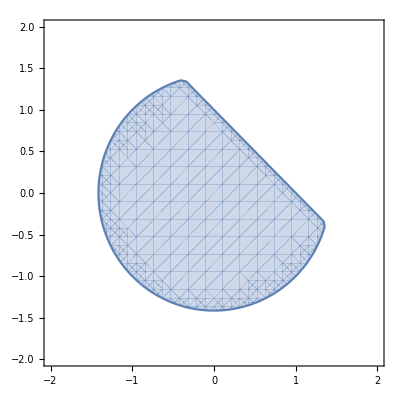

```mathematica
RegionPlot[x^2 + y^2 < 2 && x + y < 1, {x, -2, 2}, {y, -2, 2},  Axes -> True]
```

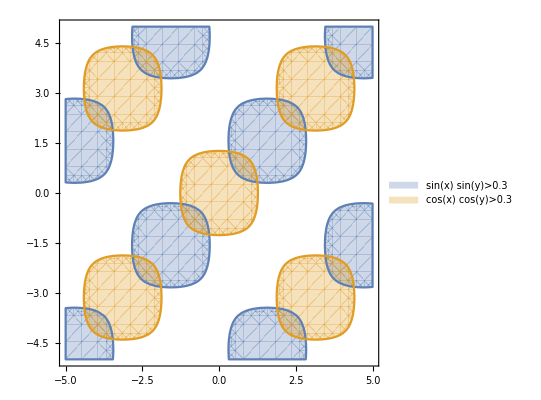

```mathematica
RegionPlot[{Sin[x] Sin[y] > 0.3, Cos[x] Cos[y] > 0.3}, {x, -5,   5}, {y, -5, 5}, PlotLegends -> "Expressions"]
```

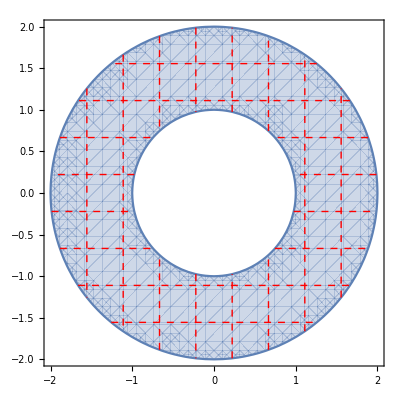

```mathematica
RegionPlot[1 < x^2 + y^2 < 4, {x, -2, 2}, {y, -2, 2}, Mesh -> 8,  MeshStyle -> Directive[Red, Dashed]]
```

```mathematica
RegionPlot3D[x + y + z < -2||x + y + z > 2, {x, -2, 2}, {y, -2,   2}, {z, -2, 2}]
```

-Graphics3D-

```mathematica
RegionPlot3D[ x^2 + y^2 + z^2 < 1 && x^2 + y^2 < z^2, {x, -1, 1}, {y, -1,   1}, {z, -1, 1}, PlotPoints -> 35, PlotRange -> All]
```

-Graphics3D-

### 3. 向量图和流量图

VectorPlot[{vx, vy}, {x, xmin, xmax}, {y, ymin, ymax}]
生成以 x 和 y 的函数表示的矢量场 {vx, vy} 的矢量图.

VectorPlot[{{vx, vy}, {wx, wy}, …}, {x, xmin, xmax}, {y, ymin, ymax}]绘制多个矢量场.

VectorPlot[…, {x, y} ∈ reg] 令变量 {x, y} 位于几何区域 reg 内.

VectorPlot3D[{vx, vy, vz}, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
生成以 x、y 和 z 的函数表示的矢量场 {vx, vy, vz} 的矢量图

VectorPlot3D[{field1, field2, …}, {x, xmin, xmax}, {y, ymin, ymax}, {z, zmin, zmax}]
绘制多个矢量图.

VectorPlot3D[…, {x, y, z} ∈ reg] 将变量 {x, y, z} 置于几何区域 reg 中.

例题

-Graphics-

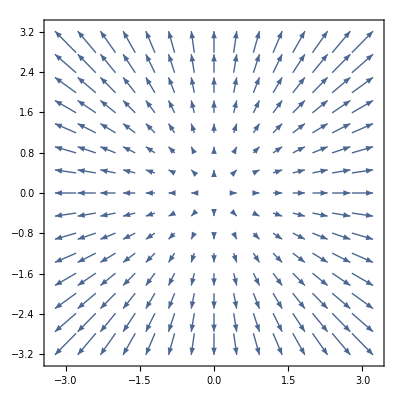
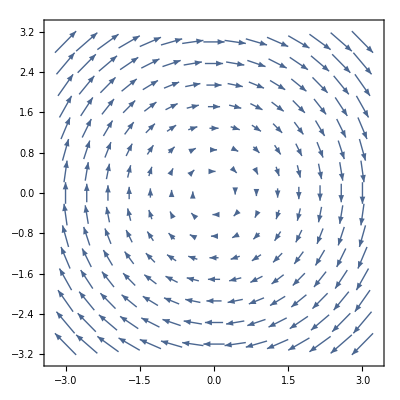

```mathematica
VectorPlot[{{x+y,y-x},{y,x+y}},{x,-3,3},{y,-3,3}]
{VectorPlot[{x, y}, {x, -3, 3}, {y, -3, 3}],VectorPlot[{y, -x}, {x, -3, 3}, {y, -3, 3}]}
```

```mathematica
VectorPlot[Evaluate[D[Cos[x +y],{{x,y}}]],{x,0,1},{y,0,1}]
```

General::ivar: {-0.8966,-0.788087,0.944525,0.546198,0.830395,0.354945,«40»,0.235606,0.0962129,0.49514,0.436239,«50»} is not a valid variable.

General::ivar: 0.0000714286 is not a valid variable.

General::ivar: 0.0715 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
VectorPlot3D[{z, x, x + y}, {x, -1, 1}, {y, -1, 1}, {z, -1, 1}]
```

-Graphics3D-

选项

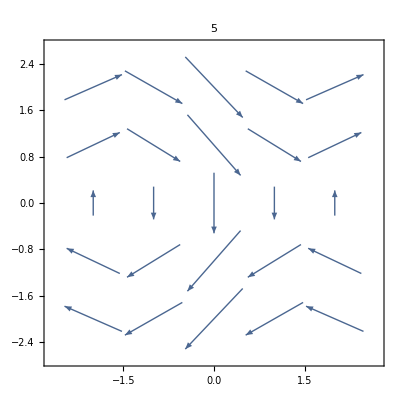
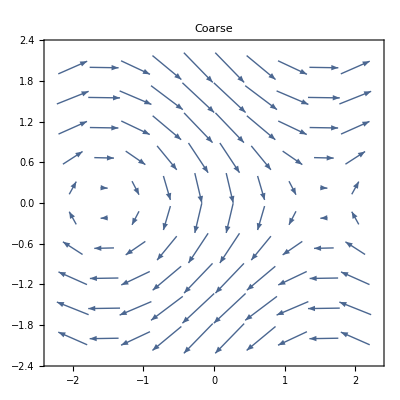
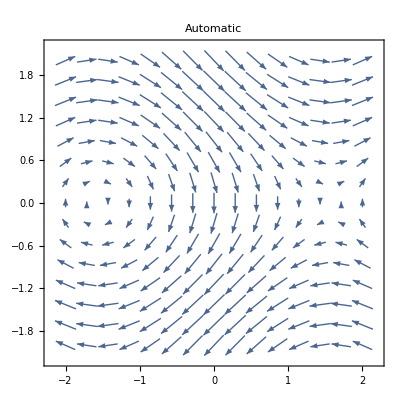
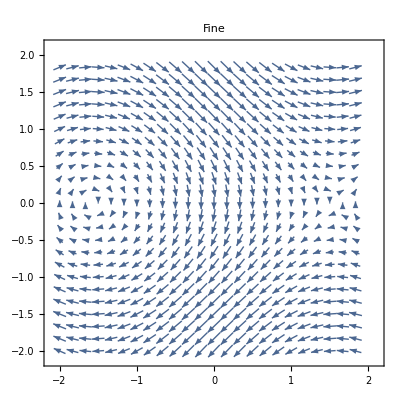

```mathematica
Table[VectorPlot[{Sin[y], -Cos[x]}, {x, -2, 2}, {y, -2, 2},   PlotLabel -> k,   VectorPoints -> k], {k, {5, Coarse, Automatic, Fine}}]
```

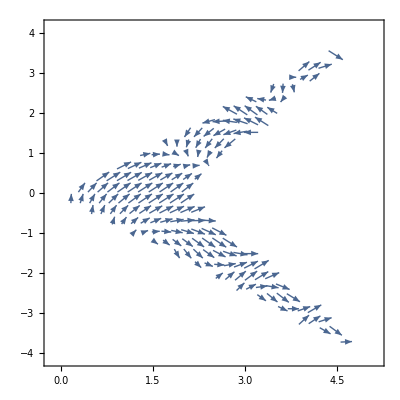

```mathematica
reg=MeshRegion[{{0,0},{5,-4},{2,0},{5,4}},Polygon[{1,2,3,4}]];
VectorPlot[{Sin[x+y],Cos[x y]},{x,y}∈reg, VectorPoints -> 30]
```

设定颜色

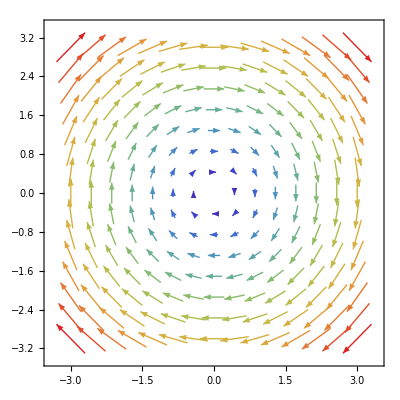

```mathematica
VectorPlot[{y, -x }, {x, -3, 3}, {y, -3, 3}, VectorScale -> Large,  VectorColorFunction -> "Rainbow"]
```

向量标记

```mathematica
VectorPlot[{{-1 - x^2 + y,  1 + x - y^2}, {-(1 + x - y^2), -1 - x^2 + y}}, {x, -3, 3}, {y, -3,   3}, VectorColorFunction -> None,  VectorStyle -> {{Orange, "Drop"}, {Blue, "Dart"}}]
```

-Graphics-

组合图形

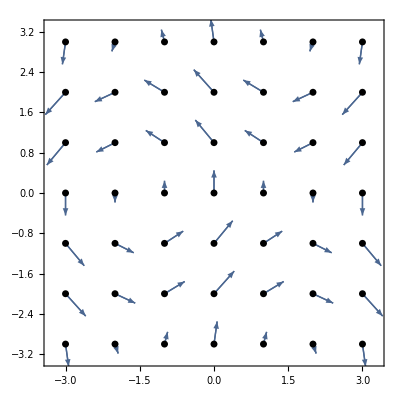

```mathematica
pts = Tuples[Range[-3, 3], 2];
VectorPlot[{-Sin[y], Cos[x]}, {x, -3, 3}, {y, -3, 3},  VectorMarkers -> Placed["Arrow", "Start"], VectorPoints -> pts,  Epilog -> {AbsolutePointSize[5], Black, Point[pts]}]
```

StreamPlot[{vx, vy}, {x, xmin, xmax}, {y, ymin, ymax}]
生成以 x 和 y 的函数表示的矢量场 {vx, vy} 的流线图.

StreamPlot[{{vx, vy}, {wx, wy}, …}, {x, xmin, xmax}, {y, ymin, ymax}]
绘制多个矢量场.

StreamPlot[…, {x, y} ∈ reg] 认为变量 {x, y} 位于几何区域 reg 中.

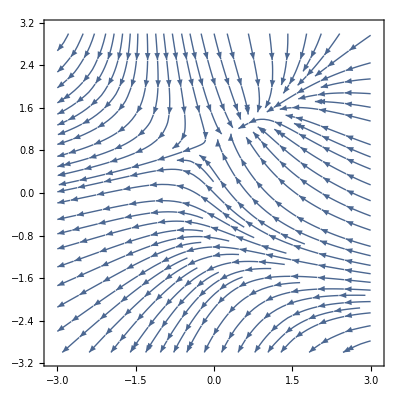

```mathematica
StreamPlot[{-1 - x^2 + y, 1 + x - y^2}, {x, -3, 3}, {y, -3, 3}]
```

将流线可视化为不间断的线条

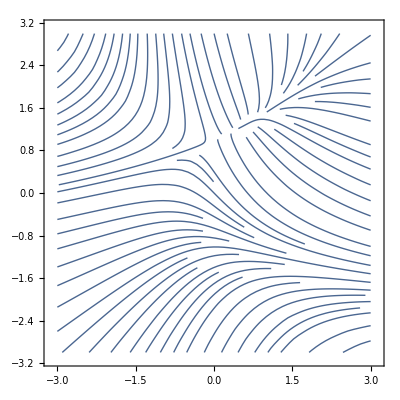

```mathematica
StreamPlot[{-1 - x^2 + y, 1 + x - y^2}, {x, -3, 3}, {y, -3, 3},  StreamScale -> None]
```

指定过某点的流线样式

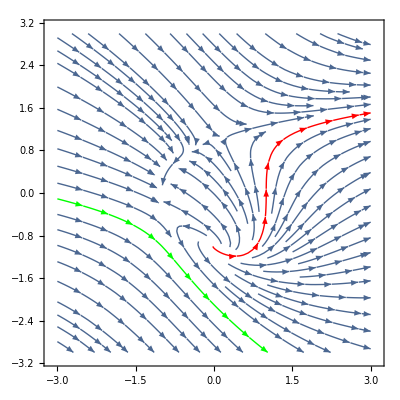

```mathematica
StreamPlot[{-1 + x^2 + y^2, 1 + x - y^2}, {x, -3, 3}, {y, -3, 3},  StreamColorFunction -> None,  StreamPoints -> {{{{1, 0}, Red}, {{-1, -1}, Green}, Automatic}}]
```

在数字赋值之前，使用 Evaluate 对矢量场进行符号式计算

```mathematica
StreamPlot[Evaluate[D[x^2  Sin[x y], {{x, y}}]], {x, 0, 1}, {y, 0, 1}]
```

General::ivar: {-0.8966,-0.788087,0.944525,0.546198,0.830395,0.354945,«40»,0.235606,0.0962129,0.49514,0.436239,«50»} is not a valid variable.

General::ivar: 0.0000714286 is not a valid variable.

General::ivar: 0.0715 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

### 4. 矩阵绘图

ArrayPlot[array]  生成一个图形，图形中数组的值以离散的方形阵列表示.

（1） 在默认情况下，ArrayPlot[array] 每页从上至下顺序设置连续的 array 行，从左至右设置连续的列，类似一个表或网格的通常格式
（2） 如果 array 含有 0 和 1，则 1 显示为黑色正方形，0 显示为白色正方形.
   ArrayPlot 缺省下以灰色输出，其中 0 值显示为白色，最大正或负值显示为黑色.

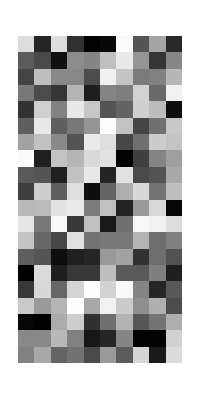

```mathematica
ArrayPlot[RandomReal[1, {20,10}]]
```

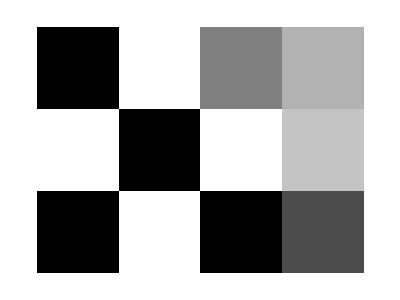

```mathematica
ArrayPlot[{{1, 0, 0.5, 0.3}, {0, 1, 0, 0.23}, {1, 0, 1, 0.7}}]
```

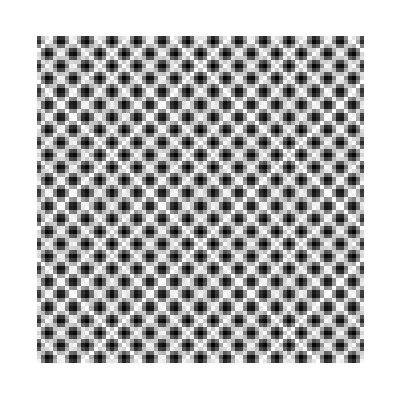

```mathematica
ArrayPlot[Table[Sin[x] + Cos[y], {x, -40, 40}, {y, -40, 40}]]
```

指定显示的颜色

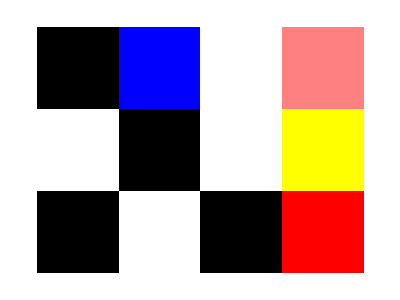

```mathematica
ArrayPlot[{{1, Blue, 0, Pink}, {0, 1, 0, Yellow}, {1, 0, 1, Red}}]
```

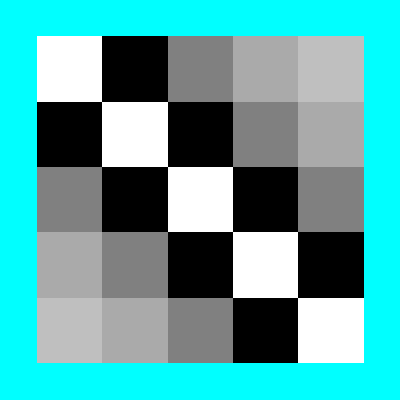

```mathematica
ArrayPlot[Table[If[x == y, None, 1/(x - y)], {x, -2, 2}, {y, -2, 2}],  Background -> Cyan]
```

array可以用第四章矩阵的定义

```mathematica
ArrayPlot[ SparseArray[{Band[{1, 1}] -> 1, Band[{2, 1}] -> 0.7,   Band[{3, 1}] -> 0.5}, {10, 10}], Mesh -> True]
```

-Graphics-

MatrixPlot[m] 绘制一个可视化描述矩阵中元素值的图形.

（1） 默认情况下，MatrixPlot[m] 向下纵向连续排列 m 行，将列横向连续排列，如同格式化普通的矩阵一样.
   （2） 默认情况下，MatrixPlot 中 0 值显示为白色，而负值则是使用 （冷色系） 蓝色表示，正值用 （暖色系） 红色表示.

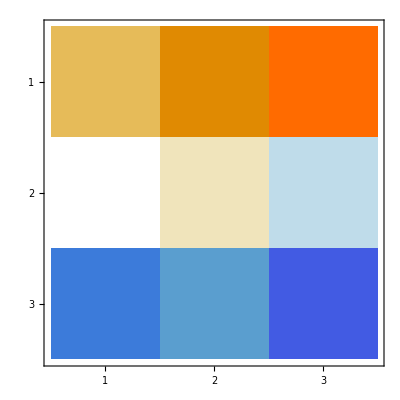

```mathematica
MatrixPlot[{{1, 2, 3}, {1.*^-16, 0.00001, -0.00001}, {-2, -1, -3}}]
```

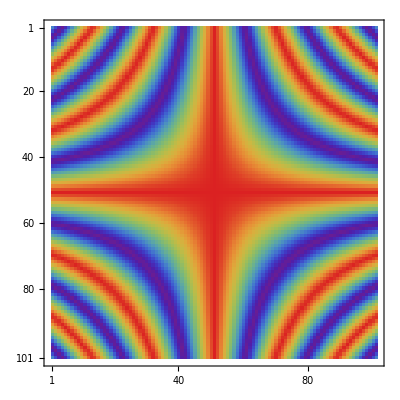

```mathematica
MatrixPlot[Table[Cos[x y/150.], {x, -50, 50}, {y, -50, 50}], 
 ColorFunction -> "Rainbow"]
```

```mathematica
6.	树形图
```

TreePlot              2007 版本中引入 (6.0) | 2019 版本中被更新 (12.0) ▪ 2020 (12.1)

TreePlot[g]     产生图 g 的树图.

TreePlot[{e1, e2, …}]  产生边为 ej 的树图.

TreePlot[{…, w[ei], …}]    绘制特征由符号封装 w 定义的 ei.

TreePlot[{vi 1 -> vj 1, …}] 使用规则 vi 1 -> vj 1 指定图 g.

TreePlot[m]   产生由邻接矩阵 m 表示的树图.

TreePlot[…, v -> pos] 将根 v 放在图的位置 pos.

以下封装可以用在边ei

Annotation[ei, label]提供注释

Button[ei, action]定义当点击元素时执行的行为

EventHandler[ei, …]定义元素的一般事件句柄

Hyperlink[ei, uri]把元素作为超链接

Labeled[ei, …]显示带有标签的元素

PopupWindow[ei, cont]在元素上附加弹出窗口

StatusArea[ei, label]当鼠标悬停在元素时显示在状态区

Style[ei, opts]使用指定的样式显示元素

Tooltip[ei, label]在元素上附加任意的提示条

#### 可用选项

DataRange                      Automatic                      生成顶点坐标的范围

DirectedEdges               False                                 是否把 Rule 诠释为 DirectedEdge

EdgeLabels                     None                                边的标签和位置

EdgeLabelStyle             Automatic                       边标签使用的样式

EdgeShapeFunction    Automatic                       产生边的图形状

EdgeStyle                        Automatic                       边的样式

GraphHighlight             {}	                                       突出显示的顶点和边

GraphHighlightStyle   Automatic                       突出显示的样式

LayerSizeFunction       (1)	                       每一层允许的高度

PerformanceGoal        Automatic                       试图最优化的性能方面

PlotStyle                         Automatic                       对顶点和边的整体图形指令

PlotTheme                     Automatic                       图的整体主题

VertexCoordinates       Automatic                       顶点的坐标

VertexLabels                   None                                 顶点的标签和位置

VertexLabelStyle           Automatic                       用于顶点标签的样式

VertexShape                    Automatic                      顶点的图形形状

VertexShapeFunction   Automatic                     产生顶点的图形形状

VertexSize                         Automatic                      顶点的大小

VertexStyle                       Automatic                     顶点的样式

(1) 给出边的规则

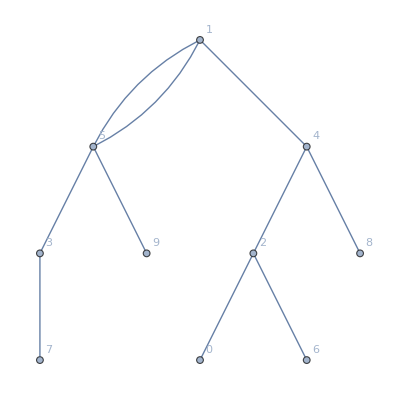

```mathematica
TreePlot[{1 -> 5, 2 -> 0, 3 -> 5, 4 -> 2, 5 -> 1, 6 -> 2, 7 -> 3, 
  8 -> 4, 9 -> 5, 4 -> 1}, VertexLabels -> Automatic]
```

(2) 给邻接矩阵

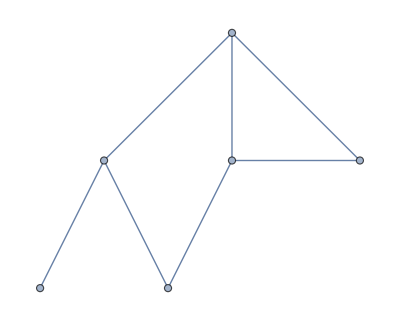

```mathematica
TreePlot[{{0, 1, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1}, {0, 0, 0, 1, 0,   1}, {0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}}]
```

(3) 选取不同的根结点

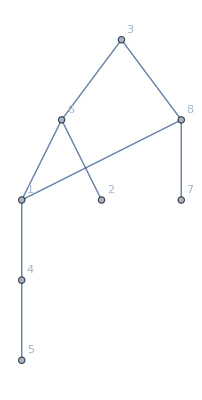
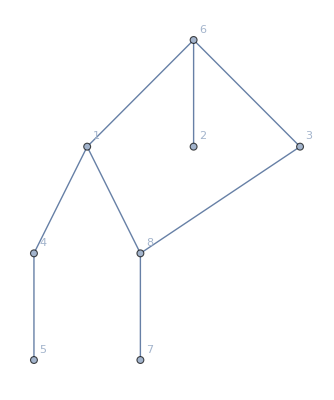
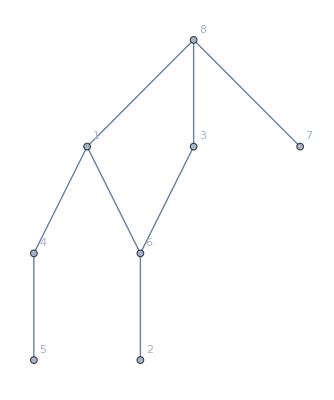

```mathematica
Table[TreePlot[{1 -> 4, 1 -> 6, 1 -> 8, 2 -> 6, 3 -> 6, 8 -> 3,    4 -> 5, 7 -> 8}, Automatic, root,   VertexLabels -> Automatic], {root, {3, 6, 8}}]
```

(4) 根结点不同朝向

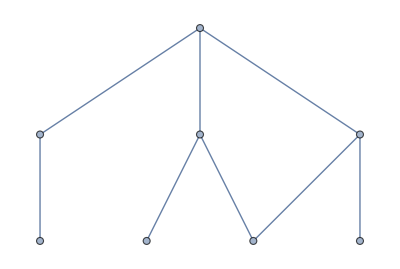
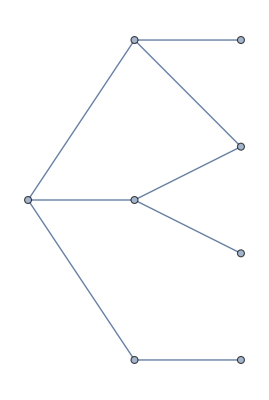
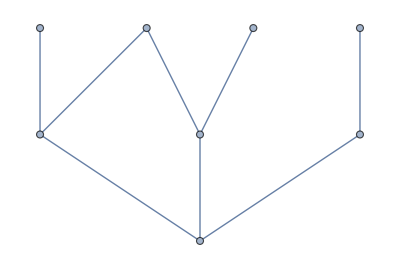
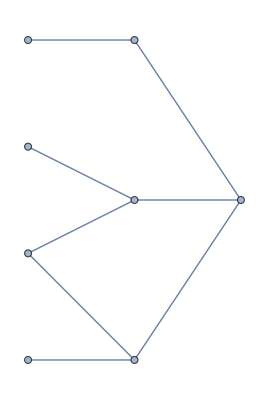
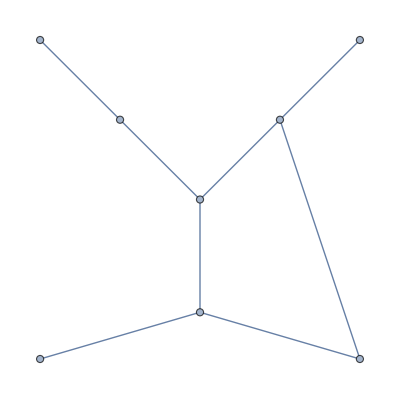

```mathematica
Table[TreePlot[{1 -> 4, 1 -> 6, 1 -> 8, 2 -> 6, 3 -> 6, 8 -> 3,    4 -> 5, 7 -> 8}, p], {p, {Top, Left, Bottom, Right, Center}}]
```

(5) 给结点标记

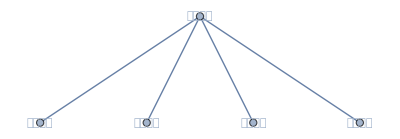

```mathematica
a=Framed["数学学院"]; b="基础数学";
c="计算数学"; d="应用数学";e="金融数学";
TreePlot[{a->b,a->c,a->d,a->e},VertexLabels->Placed[Automatic,Center]]
```

(6) 边有箭头方向

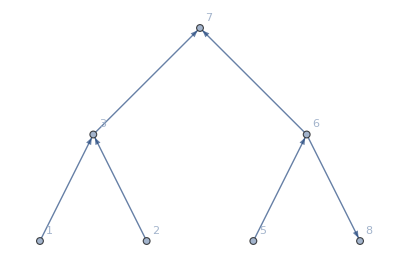

```mathematica
TreePlot[{1 -> 3, 2 -> 3, 3 -> 7, 5 -> 6, 6 -> 7, 6 -> 8},  DirectedEdges -> True, VertexLabels -> Automatic]
```

(6)	绘制2叉树

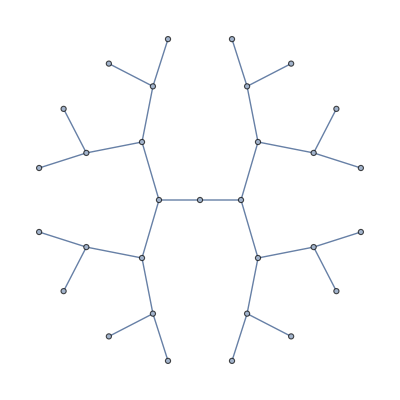

```mathematica
TreePlot[KaryTree[31, 2], Center]
```

#### TreeGraph 2010 版本中引入 (8.0) | 2015 版本中被更新 (10.3)

TreeGraph[{v1, v2, …}, {u1, u2, …}] 生成一个树，其中 ui 是 vi 的前驱.

TreeGraph[{e1, e2, …}] 产生一棵边为 ej 的树.

TreeGraph[{v1, v2, …}, {e1, e2, …}] 产生一棵顶点为 vi 边为 ej 的树.

TreeGraph[{…, wi[vi, …], …}, {…, wj[ej, …], …}]
产生一棵树，其中顶点和边的属性由符号封装 wk 定义.

TreeGraph[{vi -> vj, …}] 用规则 vi -> vj 指定树.

注意，只能生成树图

```mathematica
TreeGraph[{1 -> 2, 1 -> 3,  2 -> 4, 3-> 4}]
```

TreeGraph[{1->2,1->3,2->4,3->4}]

### 7. 图论

Graph[{e1, e2, …}]  产生具有边 ej 的图.

Graph[{v1, v2, …}, {e1, e2, …}]   产生具有顶点 vi 和边 ej 的图.

Graph[{…, wi[vi, …], …}, {…, wj[ej, …], …}]
产生具有由符号封装 wk 定义的顶点和边属性的图.

Graph[data]    由 data 生成图.

GraphPlot[g]   产生图 g 的图线.

GraphPlot[{e1, e2, …}]      绘制边为 ei 的图.

GraphPlot[{…, w[ei], …}] 绘制带有由符号封装 w 定义的特色的 ei.

GraphPlot[{vi 1 -> vj 1, …}] 使用规则 vik -> vjk 指定图 g.

GraphPlot[m] 使用邻接矩阵 m 指定图 g.

#### 说明：

（1） Graph[…] 总是转化为具有结构 Graph[vertices, edges, …] 的优化标准形式.

（2） u 和 v 之间的一条无向边可以由 u <-> v、u <-> v、UndirectedEdge[u, v] 或者 TwoWayRule[u, v] 给出. 字符 <-> 可以输入为 Esc ue Esc.
    从 u 到 v 的标记边可以通过 u  v、u  v、UndirectedEdge[u, v, t] 或 DirectedEdge[u, v, t] 给出.
    从 u 到 v 的一条有向边可以以 u -> v、u -> v、DirectedEdge[u, v] 或者 Rule[u, v] 给出. 字符 -> 可以输入为Esc de Esc.

#### 对于顶点，支持如下标准属性：

VertexLabels    顶点的标签和标签位置

VertexCoordinates     顶点的中心坐标

VertexShape         顶点的形状

VertexSize    顶点的大小

VertexStyle     顶点的样式

VertexShapeFunction        顶点的形状渲染函数

VertexWeight                      顶点的权值

#### 对于边，支持如下标准属性：

EdgeLabels      边的标签和标签位置

EdgeStyle           边的样式

EdgeShapeFunction    边的形状渲染函数

EdgeWeight              边的权值

（1） 设定结点标识

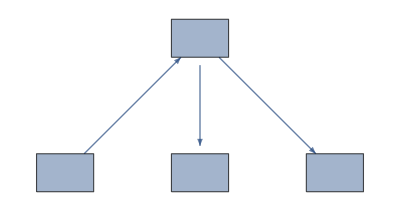

```mathematica
a="二元函数可微"; b="二元函数连续"; c="偏导数存在";d="偏导数连续";
Graph[{a->b, a->c, d->a},VertexShapeFunction->"Rectangle",VertexSize->0.4,VertexLabels->Placed[Automatic,Center]]
```

（2） 设定边的样式

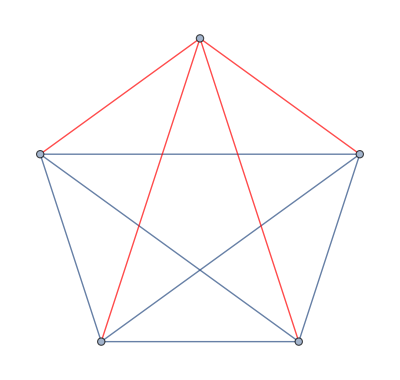
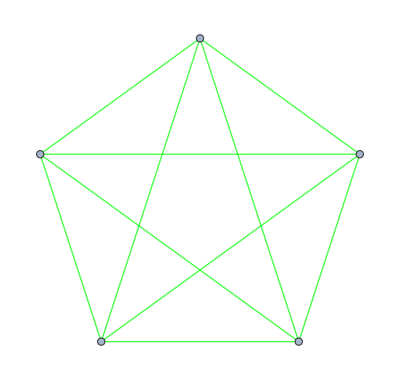
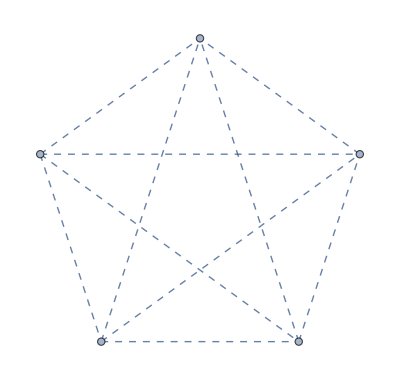

```mathematica
Table[CompleteGraph[5,   EdgeStyle -> style], {style, {_ <-> 5 -> Red, Green,    Directive[Thick, Dashed]}}]
```

（3） 用邻接矩阵画图

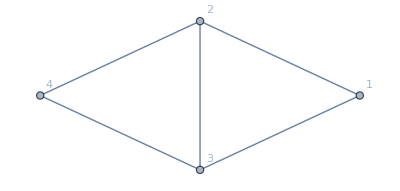

```mathematica
GraphPlot[{{0, 1, 1, 0}, {0, 1, 1, 1}, {0, 1, 0, 1}, {0, 0, 1, 1}}, 
 VertexLabels -> Automatic]
```

（4） 立体图

```mathematica
GraphPlot3D[RandomInteger[1, {7, 7}]]
```

-Graphics3D-

## §7 .3 图形动画和声音播放

### 1. 函数动画演示

Manipulate[expr, {u, umin, umax}]
产生一个带有控件的 expr 的版本，该控件允许对 u 值进行交互式操作.

Manipulate[expr, {u, umin, umax, du}] u 值在 umin 和 umax 之间以步长 du 变化

Manipulate[expr, {{u, uinit}, umin, umax, …}] u 的初始值设置为 uinit.

Manipulate[expr, {{u, uinit, ulbl}, …}]  以 ulbl 作为 u 的控件标签.

Manipulate[expr, {u, {u1, u2, …}}] 允许 u 取离散值 u1, u2, ….

Manipulate[expr, {u, …}, {v, …}, …] 使控件可以操纵每个 u, v, ….

```mathematica
Manipulate[Plot[Sin[a* x],{x,0,2Pi}],{a,1, 5}]
Manipulate[Factor[x^n -y^n], {n, 10, 100, 1}]
```

(1) Manipulate 可用于构建有任意数量控件的交互式模型.如要控制有多个参数的模
型， 只需引入新的参数及其相应的参数规范.

```mathematica
Manipulate[ Plot[ Sin[a*x + ϕ], {x, 0, 2 Pi}], {a, 1, 5}, {ϕ, 1, 10}]
```

(2) Manipulate 可用于为参数提供离散的数值列表， 而非数值的连续范围.例如， Sin 指令可被替换为一个新参数 function, 然后可给出选择列表作为 function 的参数规范

```mathematica
Manipulate[Plot[function[a* x+ϕ],{x,0,2 Pi}],{a,1,5},{ϕ,1,10},{function,{Sin,Cos,Tan}}]
Manipulate[ Plot[function[a*x + ϕ], {x, 0, 2 Pi}], {a, 1, 5}, {ϕ, 1, 10}, {function, {Sin, Cos, Tan, Csc, Sec, Cot}}]
```

函数较多时，自动选择下拉菜单，如果你想强制Mathematica 使用某特定的控件类型， 可将 ControlType 选项设置为 Setter、 Slider、RadioButtonBar 等值

```mathematica
{Manipulate[Plot[f[x], {x, 0, 2 Pi}], {f, {Sin, Cos, Tan, Cot}}],  Manipulate[ Plot[f[x], {x, 0, 2 Pi}], {f, {Sin, Cos, Tan, Cot}, 
   ControlType -> PopupMenu}]}
```

(3) 控件添加标签 : 标签输入格式为
    {{parameter, initial value, "parameter label''}, minimum, maximum}

```mathematica
Manipulate[ Plot[Sin[2Pi a x + b], {x, 0, 6}], {{a, 2, "频率"}, 1, 4}, {{b, 0, "相位"}, 
  0, 10}]
```

```mathematica
Manipulate[Plot[Sin[f* x+ ps],{x,0,2Pi},
PlotLabel->"sin("<>ToString[f] <>" x+ "<>ToString[ps]<> ")"],
{{f,1,"frequency"},1,5,Appearance-> "Labeled"},
{{ps,1,"phase shift"},1, 6, Appearance-> "Labeled"}]
```

（4） 注意指定绘图范围

```mathematica
Manipulate[Plot[x^n Sin[x], {x, 0, 10}], {n, 1, 4}]
```

```mathematica
Manipulate[ Plot[n  x Sin[x], {x, 0, 2 Pi}, PlotRange -> {-20, 10}], {n, 1, 4}]
```

（5） 控件位置和分组

```mathematica
Manipulate[ ParametricPlot[{a1 Sin[n1 x], a2 Cos[n2 x]}, {x, 0, 20 Pi},   PlotRange -> 1, PerformanceGoal -> "Quality"],  Style["x", Bold, Medium], {{n1, 1, "Frequency"}, 1,  4}, {{a1, 1, "Amplitude"}, 0, 1}, Delimiter,  Style["y", Bold, Medium], {{n2, 5/4, "Frequency"}, 1,   4}, {{a2, 1, "Amplitude"}, 0, 1}, ControlPlacement -> Left]
```

```mathematica
Manipulate[Plot3D[Sin[a x y],{x,-2, 2},{y,-2, 2}],{a,1,5}]
```

Mathematica 的默认行为是当控件移动时最优化其行为， 然后当控件被松开时再优化其外观.这让用户和控件间有一个快速交互， 并在行为结束时给出一个好的渲染结果.但是， 如果渲染比快速交互更重要， 使用例如 PerformanceGoal 的选项可以很方便地调整其行为.

PerformanceGoal -> "Quality"

```mathematica
Manipulate[Plot3D[Sin[a x y],{x,-2, 2},{y,-2, 2}, PerformanceGoal->"Quality"],
{a,1, 5}]
```

#### Animate

Animate[expr, {u, umin, umax}]
生成一个 expr 的动画，在该动画中 u 从 umin 向 umax 连续变化.

Animate[expr, {u, umin, umax, du}] 使 u 以 du 的步长变化.

Animate[expr, {u, {u1, u2, …}}] 使 u 为不连续值 u1、u2、….

Animate[expr, {u, …}, {v, …}, …] 改变所有变量 u ， v， ….

#### 选项及 默认值

AnimationDirection      Forward                   动画的方向

AnimationRate               Automatic               使变量变化的速率

AnimationRepetitions  Infinity                      停止以前的运行次数

AnimationRunning         True                         动画是否运行

AnimationRunTime         0	                自动画上次启动运行所经过的时间

AnimationTimeIndex     Automatic             动画的时间索引，其中0为开始

AppearanceElements     Automatic            包含的控制元素

BaseStyle                            {}	                动画器的基本样式规范

DefaultDuration               5.	                以秒为单位的缺省持续时间

Deinitialization                 None                       Animate 输出被删除时计算的表达式

DisplayAllSteps                False                      是否强制显示所有不连续的步长

Exclusions                           {}	                将被排除的特定值

Initialization                       None                     首次生成输出时计算的表达式.

LabelStyle                         {}	               标签区域的样式规范

RefreshRate                       Automatic            缺省的每秒钟刷新次数

ShrinkingDelay                 Automatic            如果显示的对象变小，收缩前需要延迟多长时间

```mathematica
Animate[Plot[Sin[x + a], {x, 0, 10}], {a, 0, 5}]
```

运行后直接演示动画，除非加入选项AnimationRunning -> False

```mathematica
Table[Animate[u^2, {u, 0, 1}, AnimationRepetitions -> a, AnimationRunning -> False], {a, 1, 3}]
```

控制动画循环次数

```mathematica
Animate[Graphics[{Circle[], PointSize[0.03],    Point[{Cos[t], Sin[t]}]}], {t, 0, 2 Pi, 0.1},  AnimationRunning -> False]
```

### 2. 列表动画演示 ListAnimate

ListAnimate[{expr1, expr2, …}] 生成一个动画，其帧为连续的 expri.
   ListAnimate[list, fps] 显示每秒 fps 个帧.

```mathematica
d=Table[Plot3D[Sin[x y*t],{x,0,3},{y,0,3},PlotRange->{-1,1},Mesh->True],{t,0,3,0.1}];
```

```mathematica
ListAnimate[d]
```

```mathematica
ListAnimate[{Style["\[MathematicaIcon]", Large], "string",   Framed[x + y], Graphics[Rectangle[], ImageSize -> 20]}]
```

### 3. 声音与语言

Play[f, {t, tmin, tmax}] 以声音的波形形式播放一个函数, 它的振幅以关于时间的函数 f 给出，时间 t 位于 tmin 和 tmax 之间、并以秒为单位.

Play[{f1, f2}, {t, tmin, tmax}] 产生立体声音. 首先给出左声道.

Play[{f1, f2, …}, …] 在任意多个声道上产生声音.

```mathematica
Play[(3 + Cos[30 t])*Sin[3500 t + 2 Sin[50 t]], {t, 0, 2}]
```

```mathematica
m=512;
f[m_,t_]:=Play[{Sin[512*2^(m/12)*2 Pi*x],Sin[509*2^(m/12)*2Pi*x]},{x,0,t}];
```

```mathematica
Show[{f[0, 1], f[2, 1], f[4, 1], f[5, 1], f[7, 1], f[9, 1], f[11, 1],   f[12, 1]}]
```

Sound[primitives] 表示一个声音.

Sound[primitives, t] 指定声音持续 t.

Sound[primitives, {tmin, tmax}] 指定声音应该从时间 tmin 扩展到时间 tmax 播放.

SoundNote[pitch] 表示和指定音高相符的一个音符.

SoundNote[pitch, t] 音符持续的时间长度为 t.

SoundNote[pitch, {tmin, tmax}] 音符持续的时间间隔从 tmin 到 tmax.

SoundNote[pitch, tspec, "style"] 设置指定风格的音符.

SoundNote[pitch, tspec, "style", opts] 用指定选项渲染音符.

SoundNote[] 在默认情况下，表示用钢琴演奏的中央 C 音，演奏时长为 1 秒.

```mathematica
Sound[SoundNote["C", 1, "Violin"]]
```

```mathematica
Sound[SoundNote[{"C", "G"}, 1, "Harpsichord"]]
```

```mathematica
Sound[{SoundNote[], SoundNote[4], SoundNote[7], SoundNote[12]}]
```

```mathematica
Sound[{SoundNote["C", 0.2], SoundNote[None, 0.2],   SoundNote["G", 0.3]}]
```

```mathematica
Sound[SoundNote[#, 1, RandomChoice[{"Piano", "Cello", "Tuba"}]] & /@   RandomInteger[12, 30], 4]
```

使用函数 Sound[ Play[ ], Play[ ]， •••] 播放在一起的多个声音

```mathematica
Sound[{Play[Sin[300 t Sin[20 t]], {t, 0, 1}],   Play[Sin[2000 t], {t, 1, 2}],   Play[Sin[2000 (1 + Round[2 t, 0.1]) t], {t, 2, 4}],   Play[Sign[Sin[1000 t]], {t, 0, 1}]}]
```

Speak[expr] 播放 expr 的语音表示.

Speak["string"] 播放 "string" 中的文本.

Speak[expr] 对数学表达式、程序、图形和其它结构起作用.

Speak[HoldForm[expr]] 播放 expr 的 持有形式，并不计算表达式.

```mathematica
Speak["Mathematica在各行各业有广泛的应用"]
```

```mathematica
Speak[Sin[x]^2 + Cos[x]^2]
```

```mathematica
SpokenString[Sin[x]^2 + Cos[x]^2]
```

```mathematica
Button["press ", Speak["It is wonderful"]]
```

### 4. 图形输入输出及图形处理

文件导入 Import[sourse]
ImageConvolve[image, ker]，对图像进行滤波处理, 给出 image 与内核 ker 的卷积.

```mathematica
g=Import["ExampleData/rose.gif"]
```

```mathematica
Import["ExampleData/rose.gif", "ImageSize"]
```

```mathematica
EdgeDetect[g]
```

```mathematica
Rasterize[g, RasterSize->80]
```

文件导出 Export["file", 图形]

```mathematica
g=Plot[Sin[x] + Sin[Sqrt[2] x], {x, 0, 10}]
Export["sinplot.jpg", g]
```